## Cycloid

```mathematica
$Assumptions = y > 0 && t > 0;
```

```mathematica
Off[PossibleZeroQ::ztest1];
ϕ = (x - ArcCos[1-y] +Sqrt[y(2-y)])/.{y->(y-s)};
dϕ = D[ϕ, {{x,y}}]/.{s->t};
ϕs = D[ϕ, s]/.{s->t};
v = dϕ ϕs/(Norm[dϕ]^2)//Simplify
```

{(-t+y)/(√(1-(1+t-y)^2) (1+Abs[(t-y)/(√(1-(1+t-y)^2))]^2)),(t-y)/((2+t-y) (1+Abs[(t-y)/(√(1-(1+t-y)^2))]^2))}

```mathematica
Solve[ ϕ == 0, y]
```

Solve[x+√((2+s-y) (-s+y))-ArcCos[1+s-y]==0,y]

## Double Pendulum

```mathematica
ClearAll[s,v,v2,v1perp,v1par, m1,m2,l,θ,ϕ,sols,sol];
$Assumptions=θ ∈Reals && ϕ∈Reals && l>0 && v ∈Reals && m1>0 && m2>0 ;
```

### Generate Normal Vector Field

```mathematica
v1par = v Cos[θ];
v2 = v1par Cos[ϕ-θ]-v1perp Sin[ϕ-θ];
Solve[D[ (1/2)(m2 v2^2 + m1 v1par^2+m1 v1perp^2),v1perp]== 0, v1perp];
v1perp = (v1perp/.%)[[1]];
v2 = v1par Cos[ϕ-θ]-v1perp Sin[ϕ-θ];
```

### Global Parameters

```mathematica
m1=m2=l=1;
s = t;
v=D[s,t];
```

```mathematica
v1perp = v1perp/.{θ->θ[t],ϕ->ϕ[t]};
v1par = v1par/.{θ->θ[t],ϕ->ϕ[t]};
v2 = v2/.{θ->θ[t],ϕ->ϕ[t]};
```

### Equations of Motion and Solutions

```mathematica
eqs = { 
θ'[t] ==v Sin[θ[t]] - v1perp , 
ϕ'[t]== v1par Sin[ϕ[t]-θ[t]]+v1perp Cos[ϕ[t]-θ[t]]
};
```

```mathematica
sols = Table[
NDSolve[Join[eqs, { θ[0] == ξ, ϕ[0] == η}], {θ,ϕ}, {t, -4Pi,4Pi}],
{ξ , {Pi/3, Pi/4, Pi/6, Pi/8}},{η , {Pi/3, Pi/4, Pi/6, Pi/8}}];
```

## Figures

```mathematica
pivot[t_] = { 0, s};
bob1[t_] = {Sin[θ[t]], s +Cos[θ[t]]};
bob2[t_] = bob1[t] + { Sin[ϕ[t]], Cos[ϕ[t]]};
```

```mathematica
(*frame[t_] = Graphics[{
Blue, Disk[pivot[t], .05],
Red,Disk[bob1[t],.075], 
Black,Thick,Line[{pivot[t],bob1[t]}],
Red, Disk[bob2[t],.075],
Black,Thick,Line[{bob1[t],bob2[t]}]
}];
GraphicsGrid[
Table[
Show[{
ParametricPlot[{
{Sin[θ[t]], s + Cos[θ[t]]}/.sols[[i]][[j]],{Sin[θ[t]] + Sin[ϕ[t]], s+ Cos[θ[t]] + Cos[ϕ[t]]}/.sols[[i]][[j]]}, 
{t, 0, 2Pi}
],
frame[0]/.sols[[i]][[j]],
frame[2]/.sols[[i]][[j]]
},
PlotRange->axis,
AxesOrigin->{0,0}
],
{i, 1, 4},{j, 1, 4}
]
]*)
```

### Format Plots

```mathematica
color1 = Cyan;
color2 = Magenta;
thickness = .01;
disksize = .05;
axis = {{-0.5,2.5},{-.5,2.5}};
time = 2;
```

### Plot Figures

```mathematica
frameWithDisks[t_] = Graphics[{
Blue, Disk[pivot[t], disksize],
Red,Disk[bob1[t],disksize], 
Black,Line[{pivot[t],bob1[t]}],
Red, Disk[bob2[t],disksize],
Black,Line[{bob1[t],bob2[t]}]
}];
```

```mathematica
frameNoDisks[t_] = Graphics[{
Black,Line[{pivot[t],bob1[t]}],
Black,Line[{bob1[t],bob2[t]}]
}];
```

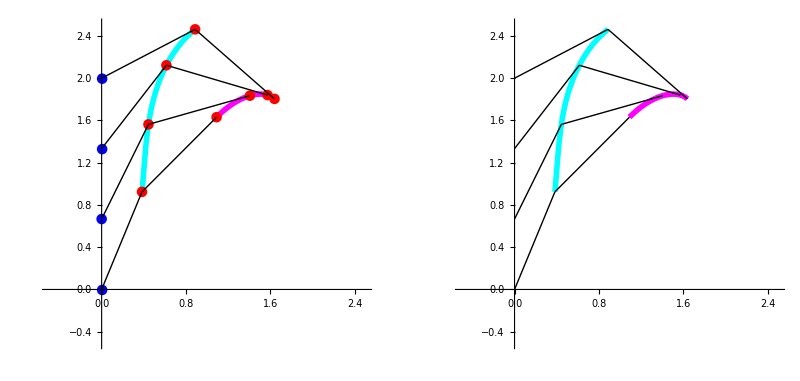

```mathematica
GraphicsRow[{
Show[{
ParametricPlot[{
{Sin[θ[t]], s + Cos[θ[t]]}/.sols[[4]][[2]],{Sin[θ[t]] + Sin[ϕ[t]], s+ Cos[θ[t]] + Cos[ϕ[t]]}/.sols[[4]][[2]]}, 
{t, 0, time},
PlotRange->axis,
AxesOrigin->{0,0},
PlotStyle->{{Thickness[thickness],color1},{ Thickness[thickness],color2}}
],
frameWithDisks[0]/.sols[[4]][[2]],
frameWithDisks[2/3]/.sols[[4]][[2]],
frameWithDisks[4/3]/.sols[[4]][[2]],
frameWithDisks[2]/.sols[[4]][[2]]
}
],
Show[{
ParametricPlot[{
{Sin[θ[t]], s + Cos[θ[t]]}/.sols[[4]][[2]],{Sin[θ[t]] + Sin[ϕ[t]], s+ Cos[θ[t]] + Cos[ϕ[t]]}/.sols[[4]][[2]]}, 
{t, 0, time},
PlotRange->axis,
AxesOrigin->{0,0},
PlotStyle->{{Thickness[thickness],color1},{ Thickness[thickness],color2}}
],
frameNoDisks[0]/.sols[[4]][[2]],
frameNoDisks[2/3]/.sols[[4]][[2]],
frameNoDisks[4/3]/.sols[[4]][[2]],
frameNoDisks[2]/.sols[[4]][[2]]
}
]
}
]
```

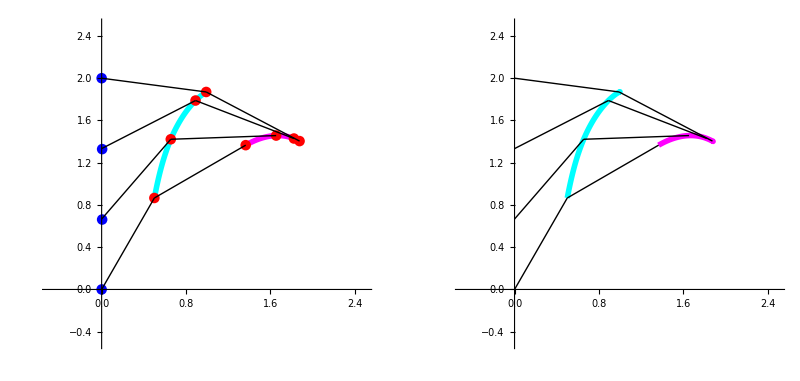

```mathematica
GraphicsRow[{
Show[{
ParametricPlot[{
{Sin[θ[t]], s + Cos[θ[t]]}/.sols[[3]][[1]],{Sin[θ[t]] + Sin[ϕ[t]], s+ Cos[θ[t]] + Cos[ϕ[t]]}/.sols[[3]][[1]]}, 
{t, 0, 2},
PlotRange->axis,
AxesOrigin->{0,0},
PlotStyle->{{Thickness[thickness],color1},{ Thickness[thickness],color2}}
],
frameWithDisks[0]/.sols[[3]][[1]],
frameWithDisks[2/3]/.sols[[3]][[1]],
frameWithDisks[4/3]/.sols[[3]][[1]],
frameWithDisks[2]/.sols[[3]][[1]]
}
],
Show[{
ParametricPlot[{
{Sin[θ[t]], s + Cos[θ[t]]}/.sols[[3]][[1]],{Sin[θ[t]] + Sin[ϕ[t]], s+ Cos[θ[t]] + Cos[ϕ[t]]}/.sols[[3]][[1]]}, 
{t, 0, 2},
PlotRange->axis,
AxesOrigin->{0,0},
PlotStyle->{{Thickness[thickness],color1},{ Thickness[thickness],color2}}
],
frameNoDisks[0]/.sols[[3]][[1]],
frameNoDisks[2/3]/.sols[[3]][[1]],
frameNoDisks[4/3]/.sols[[3]][[1]],
frameNoDisks[2]/.sols[[3]][[1]]
}
]
}
]
```

## Animation

```mathematica
axis = {{-0.5,2},{-1,5}};
endtime = 4;
duration = 3;
initθ = Pi/6;
initϕ = Pi/4;
```

```mathematica
sol = 
NDSolve[Join[eqs, { θ[0] == initθ, ϕ[0] == initϕ}], {θ,ϕ}, {t, -4Pi,4Pi}];
```

```mathematica
pivot[t_] = { 0, s};
bob1[t_] = {Sin[θ[t]], s +Cos[θ[t]]};
bob2[t_] = bob1[t] + { Sin[ϕ[t]], Cos[ϕ[t]]};
```

```mathematica
animationFrame[t_] = Graphics[{
Blue, Disk[pivot[t], .05],
Red,Disk[bob1[t],.075], 
Black,Thick,Line[{pivot[t],bob1[t]}],
Red, Disk[bob2[t],.075],
Black,Thick,Line[{bob1[t],bob2[t]}]
}];
frames = Table[Show[
ParametricPlot[ {{Sin[θ[t]], s+Cos[θ[t]]}/.sol,{ Sin[θ[t]] + Sin[ϕ[t]], s+ Cos[θ[t]] + Cos[ϕ[t]]}/.sol}, {t, -1, τ}],
animationFrame[τ]/.sol,
PlotRange->axis,
AxesOrigin->{0,0}
],{τ,0,endtime,.1}];
```

```mathematica
ListAnimate[frames,DefaultDuration->duration]
```